```mathematica
rgbc1=1/65536 Partition[{0,0,0,0,93,468,0,187,936,0,280,1404,0,374,1872,0,467,2340,0,561,2808,0,655,3276,0,748,3744,0,842,4212,0,935,4680,0,1029,5148,0,1122,5616,0,1216,6084,0,1310,6553,0,1310,6553,0,1387,6938,0,1464,7323,0,1541,7709,0,1618,8094,0,1695,8480,0,1772,8865,0,1849,9251,0,1926,9636,0,2003,10022,0,2080,10407,0,2157,10793,0,2234,11178,0,2311,11564,0,2388,11949,0,2465,12335,0,2542,12720,0,2620,13106,0,2621,13107,0,3884,14464,0,5148,15822,0,6412,17179,0,7676,18537,0,8940,19894,0,10204,21252,0,11468,22609,0,12731,23967,0,13995,25324,0,15259,26682,0,16523,28039,0,17787,29397,0,19051,30754,0,20315,32112,0,20315,32112,0,21625,33469,0,22936,34827,0,24246,36184,0,25557,37542,0,26868,38899,0,28178,40257,0,29489,41614,0,30800,42972,0,32110,44329,0,33421,45687,0,34732,47044,0,36042,48402,0,37353,49759,0,38664,51117,0,38665,51117,1485,39451,50854,2970,40237,50592,4456,41024,50330,5941,41810,50068,7427,42597,49806,8912,43383,49544,10397,44169,49282,11883,44956,49019,13368,45742,48757,14854,46529,48495,16339,47315,48233,17824,48101,47971,19310,48888,47709,20795,49674,47447,22281,50461,47185,22281,50461,47185,23632,51239,46939,24984,52017,46693,26335,52795,46447,27687,53573,46202,29039,54351,45956,30390,55130,45710,31742,55908,45464,33094,56686,45219,34445,57464,44973,35797,58242,44727,37148,59021,44481,38500,59799,44236,39852,60577,43990,41203,61355,43744,42555,62133,43498,43907,62912,43253,43908,62913,43253,44607,63000,43995,45306,63087,44738,46005,63175,45481,46704,63262,46223,47403,63349,46966,48102,63437,47709,48801,63524,48451,49500,63611,49194,50199,63699,49937,50898,63786,50679,51597,63873,51422,52296,63961,52165,52995,64048,52907,53694,64135,53650,54393,64223,54393,54394,64224,54394,55096,64317,55189,55798,64411,55985,56500,64504,56781,57202,64598,57576,57904,64691,58372,58606,64785,59168,59309,64879,59964,60011,64972,60759,60713,65066,61555,61415,65159,62351,62117,65253,63146,62819,65346,63942,63521,65440,64738,64224,65534,65534,17694,30801,13107,19566,30052,13107,19566,30052,13107},3];
ColFuncZmap1[m_,M_,a_]:=Function[Blend[RGBColor[#[[1]],#[[2]],#[[3]]]&/@rgbc1,((#-m)/(M-m))^a]];
```

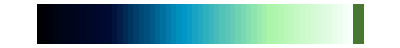

```mathematica
aab=ArrayPlot[{Table[x,{x,0,1,1/60}]},ColorFunctionScaling->False,Frame->None,AspectRatio->0.1,ColorFunction->ColFuncZmap1[0,1,.9]]
```

```mathematica
ColFunc1[m_,M_,a_]:=Function[If[((#-m)/(M-m))>0.2,Blend[{White,Blue},(((#-m)/(M-m)-0.2)/0.8)^a],White]];
```

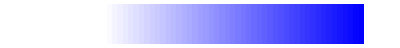

```mathematica
ArrayPlot[{Table[x,{x,0,1,1/60}]},ColorFunctionScaling->False,Frame->None,AspectRatio->0.1,ColorFunction->ColFunc1[0,1,1]]
```

```mathematica
rgbc=1/65536 Partition[{0,0,0,0,93,468,0,187,936,0,280,1404,0,374,1872,0,467,2340,0,561,2808,0,655,3276,0,748,3744,0,842,4212,0,935,4680,0,1029,5148,0,1122,5616,0,1216,6084,0,1310,6553,0,1310,6553,0,1387,6938,0,1464,7323,0,1541,7709,0,1618,8094,0,1695,8480,0,1772,8865,0,1849,9251,0,1926,9636,0,2003,10022,0,2080,10407,0,2157,10793,0,2234,11178,0,2311,11564,0,2388,11949,0,2465,12335,0,2542,12720,0,2620,13106,0,2621,13107,0,3884,14464,0,5148,15822,0,6412,17179,0,7676,18537,0,8940,19894,0,10204,21252,0,11468,22609,0,12731,23967,0,13995,25324,0,15259,26682,0,16523,28039,0,17787,29397,0,19051,30754,0,20315,32112,0,20315,32112,0,21625,33469,0,22936,34827,0,24246,36184,0,25557,37542,0,26868,38899,0,28178,40257,0,29489,41614,0,30800,42972,0,32110,44329,0,33421,45687,0,34732,47044,0,36042,48402,0,37353,49759,0,38664,51117,0,38665,51117,1485,39451,50854,2970,40237,50592,4456,41024,50330,5941,41810,50068,7427,42597,49806,8912,43383,49544,10397,44169,49282,11883,44956,49019,13368,45742,48757,14854,46529,48495,16339,47315,48233,17824,48101,47971,19310,48888,47709,20795,49674,47447,22281,50461,47185,22281,50461,47185,23632,51239,46939,24984,52017,46693,26335,52795,46447,27687,53573,46202,29039,54351,45956,30390,55130,45710,31742,55908,45464,33094,56686,45219,34445,57464,44973,35797,58242,44727,37148,59021,44481,38500,59799,44236,39852,60577,43990,41203,61355,43744,42555,62133,43498,43907,62912,43253,43908,62913,43253,44607,63000,43995,45306,63087,44738,46005,63175,45481,46704,63262,46223,47403,63349,46966,48102,63437,47709,48801,63524,48451,49500,63611,49194,50199,63699,49937,50898,63786,50679,51597,63873,51422,52296,63961,52165,52995,64048,52907,53694,64135,53650,54393,64223,54393,54394,64224,54394,55096,64317,55189,55798,64411,55985,56500,64504,56781,57202,64598,57576,57904,64691,58372,58606,64785,59168,59309,64879,59964,60011,64972,60759,60713,65066,61555,61415,65159,62351,62117,65253,63146,62819,65346,63942,63521,65440,64738,64224,65534,65534,17694,30801,13107,19566,30052,13107,21438,29303,13107,23311,28554,13107,25183,27805,13107,27056,27056,13107,28928,26307,13107,30801,25559,13107,30801,25558,13107,31893,26650,13543,32985,27742,13980,34077,28834,14417,35169,29926,14854,36261,31018,15291,37354,32111,15728,37354,32112,15728,38163,32921,15997,38973,33731,16267,39782,34540,16537,40592,35350,16807,41401,36159,17077,42211,36969,17346,43020,37778,17616,43830,38588,17886,44639,39397,18156,45449,40207,18426,46258,41016,18696,47068,41826,18965,47877,42635,19235,48687,43445,19505,49496,44254,19775,50306,45064,20045,51116,45874,20315,51117,45874,20315,52053,46810,20689,52989,47746,21063,53925,48682,21438,54861,49618,21812,55798,50555,22187,56734,51491,22561,57670,52427,22936,58606,53363,23310,59542,54299,23684,60479,55236,24059,61415,56172,24433,62351,57108,24808,63287,58044,25182,64224,58981,25557,64224,58981,25558,64224,59068,25994,64224,59155,26431,64224,59243,26868,64224,59330,27305,64224,59417,27742,64224,59505,28179,64224,59592,28616,64224,59679,29052,64224,59767,29489,64224,59854,29926,64224,59941,30363,64224,60029,30800,64224,60116,31237,64224,60203,31674,64224,60291,32111,64224,60292,32112,64270,60338,32626,64317,60385,33141,64364,60432,33656,64411,60479,34171,64457,60525,34686,64504,60572,35201,64551,60619,35716,64598,60666,36230,64645,60713,36745,64691,60759,37260,64738,60806,37775,64785,60853,38290,64832,60900,38805,64879,60947,39320,64879,60947,39321,64879,61024,39667,64879,61101,40014,64879,61178,40361,64879,61255,40708,64879,61332,41055,64879,61409,41402,64879,61486,41749,64879,61563,42096,64879,61640,42443,64879,61717,42790,64879,61794,43137,64879,61871,43484,64879,61948,43831,64879,62025,44178,64879,62102,44525,64879,62179,44872,64879,62257,45219,64879,62258,45219,64879,62398,45967,64879,62538,46716,64879,62679,47465,64879,62819,48214,64879,62960,48963,64879,63100,49712,64879,63241,50461,64879,63381,51210,64879,63521,51959,64879,63662,52708,64879,63802,53457,64879,63943,54206,64879,64083,54955,64879,64224,55704,64879,64224,55704,64922,64311,56359,64966,64398,57014,65010,64486,57670,65053,64573,58325,65097,64660,58980,65141,64748,59636,65184,64835,60291,65228,64922,60946,65272,65010,61602,65315,65097,62257,65359,65184,62912,65403,65272,63568,65446,65359,64223,65490,65446,64878,65534,65534,65534},3];
ColFuncZmap[m_,M_,a_]:=Function[Blend[RGBColor[#[[1]],#[[2]],#[[3]]]&/@rgbc,((#-m)/(M-m))^a]];
```

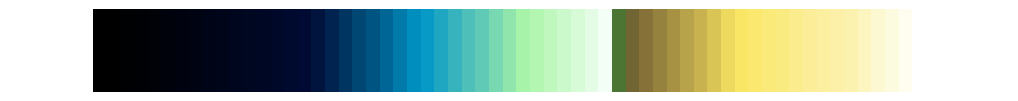

```mathematica
ArrayPlot[{Table[x,{x,0,1,1/60}]},ColorFunctionScaling->False,Frame->None,AspectRatio->0.1,ColorFunction->ColFuncZmap[0,1,1.5]]
```